Tests and Conditionals

Is 2+2 equal to 4? Let’s ask the Wolfram Language.

Test whether 2+2 is equal to 4:

```mathematica
2+2==4
```

True

Not surprisingly, testing whether 2+2 is equal to 4 gives True.

We can also test whether 2×2 is greater than 5. We do that using >.

Test whether 2×2 is greater than 5:

```mathematica
2*2>5
```

False

The function If lets you choose to give one result if a test is True, and another if it’s False.

Since the test gives True, the result of the If is x:

```mathematica
If[2+2==4,x,y]
```

x

By using a pure function with /@, we can apply an If to every element of a list.

If an element is less than 4, make it x, otherwise make it y:

```mathematica
If[#<4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,y,y,y,y}

You can also test for less than or equal using ≤, which is typed as <=.

If an element is less than or equal to 4, make it x; otherwise, make it y:

```mathematica
If[#≤ 4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,x,y,y,y}

This makes an element x only if it is equal to 4:

```mathematica
If[#== 4,x,y]&/@{1,2,3,4,5,6,7}
```

{y,y,y,x,y,y,y}

You can test whether two things are not equal using ≠, which is typed as !=.

If an element is not equal to 4, make it x; otherwise, make it y:

```mathematica
If[#≠ 4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,y,x,x,x}

It’s often useful to select elements in a list that satisfy a test. You can do this by using Select, and giving your test as a pure function.

Select elements in the list that are greater than 3:

```mathematica
Select[{1,2,3,4,5,6,7},#>3&]
```

{4,5,6,7}

Select elements that are between 2 and 5:

```mathematica
Select[{1,2,3,4,5,6,7},2≤#≤5&]
```

{2,3,4,5}

Beyond size comparisons like <, > and ==, the Wolfram Language includes many other kinds of tests. Examples are EvenQ and OddQ, which test whether numbers are even or odd. (The “Q” indicates that the functions are asking a question.)

4 is an even number:

```mathematica
EvenQ[4]
```

True

Select even numbers from the list:

```mathematica
Select[{1,2,3,4,5,6,7,8,9},EvenQ[#]&]
```

{2,4,6,8}

In this case, we don’t need the explicit pure function:

```mathematica
Select[{1,2,3,4,5,6,7,8,9},EvenQ]
```

{2,4,6,8}

IntegerQ tests whether something is an integer; PrimeQ tests whether a number is prime.

Select prime numbers:

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10},PrimeQ]
```

{2,3,5,7}

Sometimes we need to combine tests. && represents “and”, || represents “or” and ! represents “not”.

Select elements of the list that are both even and greater than 2:

```mathematica
Select[{1,2,3,4,5,6,7},EvenQ[#]&&#>2&]
```

{4,6}

Select elements that are either even or greater than 4:

```mathematica
Select[{1,2,3,4,5,6,7},EvenQ[#]||#>4&]
```

{2,4,5,6,7}

Select elements that are not either even or greater than 4:

```mathematica
Select[{1,2,3,4,5,6,7},!(EvenQ[#]||#>4)&]
```

{1,3}

There are many other “Q functions” that ask various kinds of questions. LetterQ tests whether a string consists of letters.

The space between letters isn’t a letter; nor is “!”:

```mathematica
{LetterQ["a"],LetterQ["bc"],LetterQ["a b"],LetterQ["!"]}
```

{True,True,False,False}

Turn a string into a list of characters, then test which are letters:

```mathematica
LetterQ/@Characters["30 is the best!"]
```

{False,False,False,True,True,False,True,True,True,False,True,True,True,True,False}

Select the characters that are letters:

```mathematica
Select[Characters["30 is the best!"],LetterQ]
```

{i,s,t,h,e,b,e,s,t}

Select letters that appear after position 10 in the alphabet:

```mathematica
Select[Characters["30 is the best!"],LetterQ[#]&&LetterNumber[#]>10&]
```

{s,t,s,t}

You can use Select to find words in English that are palindromes, meaning that they are the same if you reverse them.

```mathematica
Select[WordList[ ],StringReverse[#]==#&]
```

{a,aha,bib,bob,boob,civic,dad,deed,dud,ere,eve,ewe,eye,gag,gig,huh,kayak,kook,level,ma'am,madam,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,refer,rotor,sis,tat,tenet,toot,tot,tut,wow}

MemberQ tests whether something appears as an element, or member, of a list.

5 appears in the list {1,3,5,7}:

```mathematica
MemberQ[{1,3,5,7},5]
```

True

Select numbers in the range 1 to 100 whose digit sequences contain 2:

```mathematica
Select[Range[100],MemberQ[IntegerDigits[#],2]&]
```

{2,12,20,21,22,23,24,25,26,27,28,29,32,42,52,62,72,82,92}

ImageInstanceQ is a machine-learning-based function that tests whether an image is an instance of a particular kind of thing, like a cat.

Test if an image is of a cat:

```mathematica
ImageInstanceQ[-Graphics-,LinguisticAssistant]
```

True

Select images of cats:

```mathematica
Select[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},ImageInstanceQ[#,LinguisticAssistant]&]
```

{-Graphics-,-Graphics-}

Here’s a geographic example of Select: find which cities in a list are less than 3000 miles from San Francisco.

Select cities whose distance from San Francisco is less than 3000 miles:

```mathematica
Select[{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant},GeoDistance[#,LinguisticAssistant]<LinguisticAssistant&]
```

{New York City,Chicago}

Vocabulary

a==b |   | test for equality
a<b |   | test whether less
a>b |   | test whether greater
a≤b |   | test whether less or equal
a≥b |   | test whether greater or equal
If[test,u,v] |   | give u if test is True and v if False
Select[list,f] |   | select elements that pass a test
EvenQ[x] |   | test whether even
OddQ[x] |   | test whether odd
IntegerQ[x] |   | test whether an integer
PrimeQ[x] |   | test whether a prime number
LetterQ[string] |   | test whether there are only letters
MemberQ[list,x] |   | test whether x is a member of list
ImageInstanceQ[image,category] |   | test whether image is an instance of category

"13 Exercises Available"
"with 7 extras" | "Get Started »"

Test whether 123^321 is greater than 456^123. »

| Expected output: |  
  | True |

Get a list of numbers up to 100 whose digits add up to less than 5. »

| Expected output: |  
  | {1,2,3,4,10,11,12,13,20,21,22,30,31,40,100} |

Make a list of the first 20 integers, with prime numbers styled red. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20} |

Find words in WordList[ ] that both begin and end with the letter “p”. »

| Expected output: |  
  | {"pap","paperclip","parsnip","partisanship","partnership","pawnshop","payslip","peep","penmanship","pep","pickup","pileup","pimp","pip","plop","plump","polyp","pomp","poop","pop","premiership","prep","primp","professorship","prop","proprietorship","pulp","pump","pup"} |

Make a list of the first 100 primes, keeping only ones whose last digit is less than 3. »

| Expected output: |  
  | {2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541} |

Find Roman numerals up to 100 that do not contain “I”. »

| Expected output: |  
  | {"V","X","XV","XX","XXV","XXX","XXXV","XL","XLV","L","LV","LX","LXV","LXX","LXXV","LXXX","LXXXV","XC","XCV","C"} |

Get a list of Roman numerals up to 1000 that are palindromes. »

| Expected output: |  
  | {"I","II","III","V","X","XIX","XX","XXX","L","C","CXC","CC","CCC","D","M"} |

Find names of integers up to 100 that begin and end with the same letter. »

| Expected output: |  
  | {"nineteen","twenty-eight","thirty-eight","eighty-one","eighty-three","eighty-five","eighty-nine","ninety-seven"} |

Get a list of words longer than 15 characters from the Wikipedia article on words. »

| Sample expected output: |  
  | {"orthographically","multiple-morpheme","Proto-Indo-European"} |

Starting from 1000, divide by 2 if the number is even, and compute 3#+1& if the number is odd; do this repeatedly 200 times (Collatz problem). »

| Expected output: |  
  | {1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2} |

Make a word cloud of 5-letter words in the Wikipedia article on computers. »

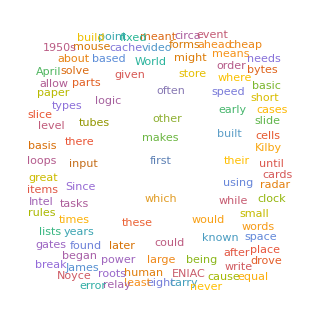
| Sample expected output: |  
  | -Graphics- |

Find words in WordList[ ] whose first 3 letters are the same as their last 3 read backward, but where the whole string is not a palindrome. »

| Expected output: |  
  | {"despised","detected","detested","drainboard","foolproof","lackadaisical","marjoram","revolver"} |

Find all 10-letter words in WordList[ ] for which the total of LetterNumber values is 100. »

| Expected output: |  
  | {"accumulate","alienation","answerable","apoplectic","aquamarine","bewitching","censurable","ceramicist","chastening","chimpanzee","clementine","clinically","collecting","condensate","congenital","conjugated","connivance","declension","deliquesce","demobilize","demodulate","denominate","diagonally","discipline","discommode","egoistical","emasculate","embodiment","emendation","empathetic","fatalistic","fatherhood","geographer","hemoglobin","impugnable","inadequacy","interbreed","leveraging","liberalism","likelihood","martingale","mercantile","meridional","neoclassic","paramecium","plebiscite","potbellied","quadrangle","reciprocal","regimented","reschedule","researcher","scoreboard","septicemia","shibboleth","sleepyhead","stagecraft","stalemated","temperance","thickening","threatened","uncombined","unmodified"} |

Make a table of integers up to 25 where every integer ending in 3 is replaced with 0. »

| Expected output: |  
  | {1,2,0,4,5,6,7,8,9,10,11,12,0,14,15,16,17,18,19,20,21,22,0,24,25} |

Use Table and If to make a 5×5 array that is 1 on its leading diagonal, and 0 otherwise.  »

| Expected output: |  
  | {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} |

Get a list of numbers up to 1000 that are equal to 1 mod both 7 and 8. »

| Expected output: |  
  | {1,57,113,169,225,281,337,393,449,505,561,617,673,729,785,841,897,953} |

Make a list of numbers up to 100, where multiples of 3 are replaced by Black, multiples of 5 by White and multiples of 3 and 5 by Red. »

| Expected output: |  
  | {1,2,GrayLevel[0],4,GrayLevel[1],GrayLevel[0],7,8,GrayLevel[0],GrayLevel[1],11,GrayLevel[0],13,14,RGBColor[1, 0, 0],16,17,GrayLevel[0],19,GrayLevel[1],GrayLevel[0],22,23,GrayLevel[0],GrayLevel[1],26,GrayLevel[0],28,29,RGBColor[1, 0, 0],31,32,GrayLevel[0],34,GrayLevel[1],GrayLevel[0],37,38,GrayLevel[0],GrayLevel[1],41,GrayLevel[0],43,44,RGBColor[1, 0, 0],46,47,GrayLevel[0],49,GrayLevel[1],GrayLevel[0],52,53,GrayLevel[0],GrayLevel[1],56,GrayLevel[0],58,59,RGBColor[1, 0, 0],61,62,GrayLevel[0],64,GrayLevel[1],GrayLevel[0],67,68,GrayLevel[0],GrayLevel[1],71,GrayLevel[0],73,74,RGBColor[1, 0, 0],76,77,GrayLevel[0],79,GrayLevel[1],GrayLevel[0],82,83,GrayLevel[0],GrayLevel[1],86,GrayLevel[0],88,89,RGBColor[1, 0, 0],91,92,GrayLevel[0],94,GrayLevel[1],GrayLevel[0],97,98,GrayLevel[0],GrayLevel[1]} |

Use Select to get a list of planets whose mass is larger than Earth. »

| Expected output: |  
  | {"Jupiter","Saturn","Uranus","Neptune"} |

Make a 50×50 array plot in which a square at position i,j is black if Mod[i,j]==0. »

| Expected output: |  
  | -Graphics- |

Make a 100×100 array plot in which a square is black if the values of both its x and y positions do not contain a 5. »

| Expected output: |  
  | -Graphics- |

Q&A

Why does one test equality with == not =?

Because = means something else in the Wolfram Language. You’ll get very strange results if you use = instead of == by mistake. (= is for assigning values of variables.) To avoid possible confusion, == is often read as “double equals”.

Why is “and” written as &&, not &?

Because & means other things in the Wolfram Language. For example it’s what ends a pure function.

How are ==, >, &&, etc. interpreted?

== is Equal, ≠ (!=) is Unequal, > is Greater, ≥ is GreaterEqual, < is Less, && is And, || is Or and ! is Not.

When do I need to use parentheses with &&, ||, etc.?

There’s an order of operations that’s a direct analog of arithmetic. && is like ×, || is like +, and ! is like −. So !p&&q means “(not p) and q”; !(p&&q) means “not (p and q)”.

What’s special about “Q” functions?

They ask a question that normally has an answer of True or False.

What are some other “Q” functions?

NumberQ, StringContainsQ, BusinessDayQ and ConnectedGraphQ are a few.

Is there a better way to find real-world entities with certain properties than using Select?

Yes. You can do things like Entity["Country","Population"→GreaterThan[10^7 "people"]] to find “implicit entities”, then use EntityList to get explicit lists of entities.

Tech Notes

True and False are typically called Booleans in computer science, after George Boole from the mid-1800s. Expressions with &&, ||, etc. are often called Boolean expressions.

In the Wolfram Language, True and False are symbols, and are not represented by 1 and 0 as in many other computer languages.

If is often called a conditional. In If[test,then,else], the then and else aren’t computed unless the test says their condition is met.

PalindromeQ directly tests if a string is a palindrome.

In the Wolfram Language, x is a symbol (see Section 33) that could represent anything, so x==1 is just an equation, that isn’t immediately True or False.  x===1 (“triple equals”) tests whether x is the same as 1, and since it isn’t, it gives False.

More to Explore

Guide to Functions That Apply Tests in the Wolfram Language »

Guide to Boolean Computation in the Wolfram Language »